```mathematica
AlphaMin=0.10;
AlphaMax=0.25;
AlphaInterval=0.01;
gfacMin=1.;
gfacMax=1.;
gfacInterval=1.;
nbasMin=9;
nbasMax=15;
nbasInterval=1;
noccMin=1;
noccMax=4;
noccInterval=1;
c0=1.0;
c1=0.5;
Table[
Table[
Table[
Table[
res[gfac][nbas][nocc][omega][alpha][c0][c1]= ReadList["/home/grining/drake-mpfun/python/results/nocc="<>ToString[nocc]<>"nbas="<>ToString[nbas]<>"omega="<>ToString[omega]<>"gfac="<>ToString[NumberForm[gfac, {2,2}]]<>"alpha="<>ToString[NumberForm[alpha, {2,2}]]<>"c0="<>ToString[NumberForm[c0, {2,2}]]<>"c1="<>ToString[NumberForm[c1, {2,2}]]<>".out_FCCD"][[1]]
,{gfac, gfacMin, gfacMax,gfacInterval}];
,{nbas, nbasMin,nbasMax,nbasInterval}];
,{nocc, noccMin,noccMax,noccInterval}];
,{omega,{9}},
{alpha,AlphaMin,AlphaMax,AlphaInterval}];
```

```mathematica
Table[
Res[nbas][nocc]=Table[
{alpha, res[1.][nbas][nocc][9][alpha][1.00][0.50]},
 {alpha,AlphaMin,AlphaMax,AlphaInterval}
],
{nocc, noccMin,noccMax,noccInterval},
{nbas, nbasMin,nbasMax,nbasInterval}
];
```

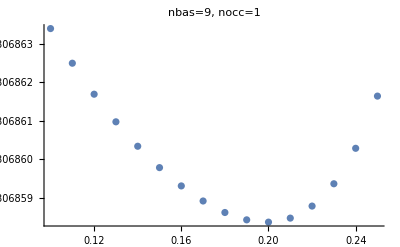
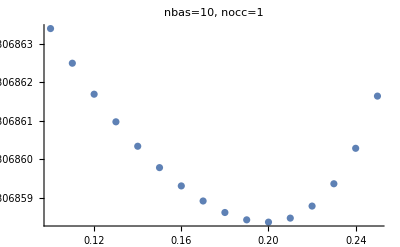
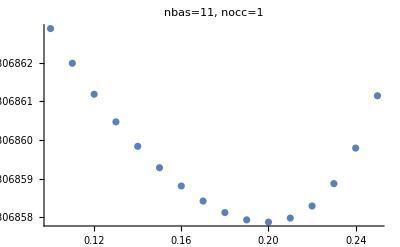
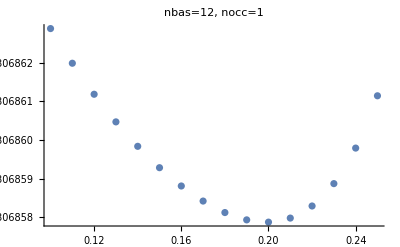
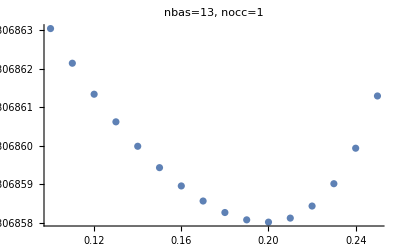
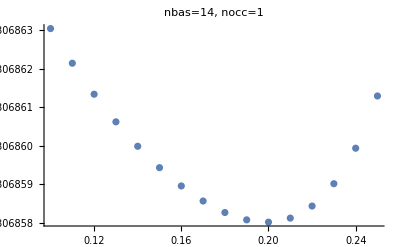
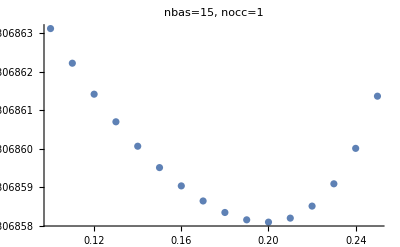
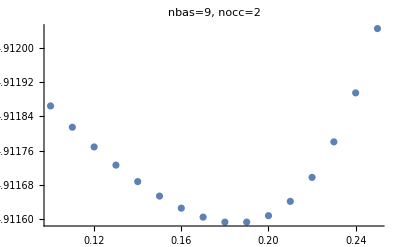

```mathematica
Table[ListPlot[Res[nbas][nocc],ImageSize->400, PlotLabel->"nbas="<>ToString[nbas]<>", nocc="<>ToString[nocc]], {nocc, noccMin,noccMax,noccInterval},{nbas, nbasMin,nbasMax,nbasInterval}]
```